## Variables

```mathematica
Clear[N1a];Clear[N1A];Clear[N2];
```

## Parameters

```mathematica
Clear[x1a];Clear[x1A];Clear[x2];Clear[xopt];
Clear[lambdaMax01];Clear[lambdaMax02];Clear[betaMax];
Clear[rMax01];Clear[rMax02];Clear[betaMax];
```

## Base equation of the discrete-time Leslie-Gower model

```mathematica
N1atPlus1=(lambdaMax01 Exp[-(x1a-xopt)^2]N1a)/(1+N1a+ Exp[-(x1A-x1a)^2]N1A+betaMax Exp[-(x2-x1a)^2] N2);
N1AtPlus1=(lambdaMax01 Exp[-(x1A-xopt)^2]N1A)/(1+N1A+ Exp[-(x1a-x1A)^2]N1a+betaMax Exp[-(x2-x1A)^2] N2);
N2tPlus1=(lambdaMax02 Exp[-(x2-xopt)^2]N2)/(1+N2+betaMax Exp[-(x1a-x2)^2]N1a+betaMax Exp[-(x1A-x2)^2] N1A);
```

## Simulation of the discrete-time Leslie-Gower model (Late immigration of sp. 2)

```mathematica
par={x1a->0.5,x1A->0,x2->-0.1,xopt->0,lambdaMax01->100,lambdaMax02->100,betaMax->1.1};
var={N1a->N1a[t],N1A->N1A[t],N2->N2[t]};
```

```mathematica
(* population dynamics *)
f1=N1atPlus1/.var;
f2=N1AtPlus1/.var;
f3=N2tPlus1/.var;
```

```mathematica
tend01=5;

(* initial values *)
init={N1a[0]==0.99(lambdaMax01 Exp[-(x1a-xopt)^2]-1/.par),N1A[0]==0.01(lambdaMax01 Exp[-(x1a-xopt)^2]-1/.par),N2[0]==0};
flow={N1a[t+1]==f1/.par,N1A[t+1]==f2/.par,N2[t+1]==f3/.par};

(* simulation *)
sol01=RecurrenceTable[Join[flow,init],{N1a,N1A,N2},{t,0,tend01}];
```

```mathematica
tend02=115;

(* initial values *)
init={N1a[0]==sol01[[tend01,1]],N1A[0]==sol01[[tend01,2]],N2[0]==(sol01[[tend01,1]]+sol01[[tend01,2]])/9};
flow={N1a[t+1]==f1/.par,N1A[t+1]==f2/.par,N2[t+1]==f3/.par};

(* simulation *)
sol02=RecurrenceTable[Join[flow,init],{N1a,N1A,N2},{t,0,tend02}];
```

```mathematica
zeroList={};Do[zeroList=Append[zeroList,0],{n,tend01+tend02}];
```

### Population dynamics

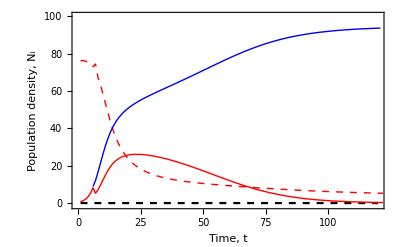

```mathematica
yMax=100;
N20List={};Do[N20List=Append[N20List,NA],{n,tend01}];

ListPlot[
{zeroList,Flatten[{ sol01[[All,1]],sol02[[All,1]]}],Flatten[{ sol01[[All,2]],sol02[[All,2]]}],Flatten[{ N20List,sol02[[All,3]]}]},Joined->True,
PlotRange-> {{0,tend01+tend02},{-1,yMax}},
PlotStyle->{{Black,Dashed},{Red,Dashed,Thick},{Red,Thick},{Blue,Thick}},Frame->True,FrameLabel->{{RawBoxes[RowBox[{RowBox[{"Population"," ","density"}],","," ",StyleBox[SubscriptBox["N","i"],FontSlant->"Italic"]}]],None},{RawBoxes[RowBox[{"Time",","," ",StyleBox["t",FontSlant->"Italic"]}]],None}},LabelStyle->{FontFamily->"Arial",18,GrayLevel[0]}
]
```

### Mean trait dynamics

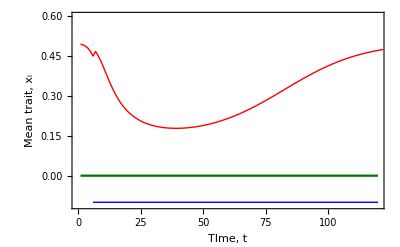

```mathematica
yMax=0.6;
x20List={};Do[x20List=Append[x20List,NA],{n,tend01}];
x21List={};Do[x21List=Append[x21List,x2/.par],{n,tend02}];
x2List=Flatten[{x20List,x21List}];

ListPlot[
{zeroList,Flatten[{(x1a/.par)sol01[[All,1]]/(sol01[[All,1]]+sol01[[All,2]]),(x1a/.par)sol02[[All,1]]/(sol02[[All,1]]+sol02[[All,2]])}],x2List},Joined->True,
PlotRange-> {{0,tend01+tend02},{-0.11,yMax}},
PlotStyle->{RGBColor[0,0.45,0],{Red,Thick},{Blue,Thick}},Frame->True,FrameLabel->{{RawBoxes[RowBox[{RowBox[{"Mean"," ","trait"}],","," ",StyleBox[SubscriptBox["x","i"],FontSlant->"Italic"]}]],None},{RawBoxes[RowBox[{"TIme",","," ",StyleBox["t",FontSlant->"Italic"]}]],None}},LabelStyle->{FontFamily->"Arial",18,GrayLevel[0]}
]
```

## Simulation of the discrete-time Leslie-Gower model (Late immigration of sp. 2)

```mathematica
par={x1a->0.5,x1A->0,x2->-0.1,xopt->0,lambdaMax01->100,lambdaMax02->100,betaMax->1.1};
var={N1a->N1a[t],N1A->N1A[t],N2->N2[t]};
```

```mathematica
(* population dynamics *)
f1=N1atPlus1/.var;
f2=N1AtPlus1/.var;
f3=N2tPlus1/.var;
```

```mathematica
tend01=10;

(* initial values *)
init={N1a[0]==0.99(lambdaMax01 Exp[-(x1a-xopt)^2]-1/.par),N1A[0]==0.01(lambdaMax01 Exp[-(x1a-xopt)^2]-1/.par),N2[0]==0};
flow={N1a[t+1]==f1/.par,N1A[t+1]==f2/.par,N2[t+1]==f3/.par};

(* simulation *)
sol01=RecurrenceTable[Join[flow,init],{N1a,N1A,N2},{t,0,tend01}];
```

```mathematica
tend02=90;

(* initial values *)
init={N1a[0]==sol01[[tend01,1]],N1A[0]==sol01[[tend01,2]],N2[0]==(sol01[[tend01,1]]+sol01[[tend01,2]])/9};
flow={N1a[t+1]==f1/.par,N1A[t+1]==f2/.par,N2[t+1]==f3/.par};

(* simulation *)
sol02=RecurrenceTable[Join[flow,init],{N1a,N1A,N2},{t,0,tend02}];
```

### Population dynamics

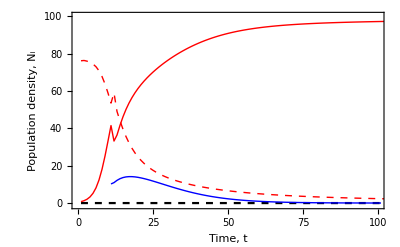

```mathematica
yMax=100;
N20List={};Do[N20List=Append[N20List,NA],{n,tend01}];

ListPlot[
{zeroList,Flatten[{ sol01[[All,1]],sol02[[All,1]]}],Flatten[{ sol01[[All,2]],sol02[[All,2]]}],Flatten[{ N20List,sol02[[All,3]]}]},Joined->True,
PlotRange-> {{0,tend01+tend02},{-1,yMax}},
PlotStyle->{{Black,Dashed},{Red,Dashed,Thick},{Red,Thick},{Blue,Thick}},Frame->True,FrameLabel->{{RawBoxes[RowBox[{RowBox[{"Population"," ","density"}],","," ",StyleBox[SubscriptBox["N","i"],FontSlant->"Italic"]}]],None},{RawBoxes[RowBox[{"Time",","," ",StyleBox["t",FontSlant->"Italic"]}]],None}},LabelStyle->{FontFamily->"Arial",18,GrayLevel[0]}
]
```

### Mean trait dynamics

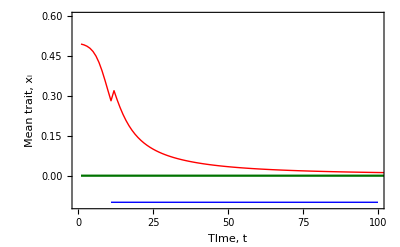

```mathematica
yMax=0.6;
x20List={};Do[x20List=Append[x20List,NA],{n,tend01}];
x21List={};Do[x21List=Append[x21List,x2/.par],{n,tend02}];
x2List=Flatten[{x20List,x21List}];

ListPlot[
{zeroList,Flatten[{(x1a/.par)sol01[[All,1]]/(sol01[[All,1]]+sol01[[All,2]]),(x1a/.par)sol02[[All,1]]/(sol02[[All,1]]+sol02[[All,2]])}],x2List},Joined->True,
PlotRange->{{0,tend01+tend02},{-0.11,yMax}},
PlotStyle->{{RGBColor[0,0.45,0]},{Red,Thick},{Blue,Thick}},Frame->True,FrameLabel->{{RawBoxes[RowBox[{RowBox[{"Mean"," ","trait"}],","," ",StyleBox[SubscriptBox["x","i"],FontSlant->"Italic"]}]],None},{RawBoxes[RowBox[{"TIme",","," ",StyleBox["t",FontSlant->"Italic"]}]],None}},LabelStyle->{FontFamily->"Arial",18,GrayLevel[0]}
]
```

## Base equation of the continuous-time Lotka-Volterra model

```mathematica
dN1adt=N1a(rMax01 Exp[-(x1a-xopt)^2]-N1a- Exp[-(x1A-x1a)^2]N1A-betaMax Exp[-(x2-x1a)^2] N2);
dN1Adt=N1A(rMax01 Exp[-(x1A-xopt)^2]-N1A- Exp[-(x1a-x1A)^2]N1a-betaMax Exp[-(x2-x1A)^2] N2);
dN2dt=N2(rMax02 Exp[-(x2-xopt)^2]-N2-betaMax Exp[-(x1a-x2)^2]N1a-betaMax Exp[-(x1A-x2)^2] N1A);
```

## Simulation of the continuous-time Lotka-Volterra model (Early immigration of sp. 2)

```mathematica
par={x1a->0.5,x1A->0,x2->-0.1,xopt->0,rMax01->100,rMax02->100,betaMax->1.1};
var={N1a->N1a[t],N1A->N1A[t],N2->N2[t]};
```

```mathematica
(* population dynamics *)
f1=dN1adt/.var;
f2=dN1Adt/.var;
f3=dN2dt/.var;
```

```mathematica
tend01=0.05;tMax=2;

(* initial values *)
init={N1a[0]==0.99(rMax01 Exp[-x1a^2]/.par),N1A[0]==0.01(rMax01 Exp[-x1a^2]/.par),N2[0]==0.};
flow={N1a'[t]==f1/.par,N1A'[t]==f2/.par,N2'[t]==f3/.par};

(* simulation *)
sol01=NDSolve[Join[flow,init],{N1a,N1A,N2},{t,0,tend01}];
```

```mathematica
tend02=tMax-tend01;

(* initial values *)
init={N1a[0]==(N1a[tend01]/.sol01)[[1]],N1A[0]==(N1A[tend01]/.sol01)[[1]],N2[0]==((N1a[tend01]/.sol01)[[1]]+(N1A[tend01]/.sol01)[[1]])/9};
flow={N1a'[t]==f1/.par,N1A'[t]==f2/.par,N2'[t]==f3/.par};

(* simulation *)
sol02=NDSolve[Join[flow,init],{N1a,N1A,N2},{t,0,tend02}];
```

### Population dynamics

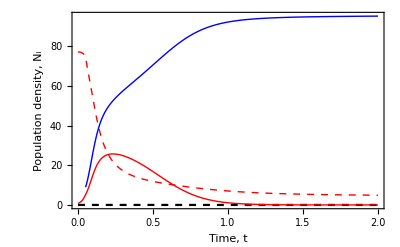

```mathematica
N1aList={};Do[N1aList=Append[N1aList,(N1a[t]/. sol01)[[1]]],{t,0,tend01,tend01/100}];
Do[N1aList=Append[N1aList,(N1a[t]/. sol02)[[1]]],{t,0,tend02,tend02/(100 tend02/tend01)}];
N1AList={};Do[N1AList=Append[N1AList,(N1A[t]/. sol01)[[1]]],{t,0,tend01,tend01/100}];
Do[N1AList=Append[N1AList,(N1A[t]/. sol02)[[1]]],{t,0,tend02,tend02/(100 tend02/tend01)}];
N2List={};
Do[N2List=Append[N2List,NA],{t,0,tend01,tend01/100}];
Do[N2List=Append[N2List,(N2[t]/. sol02)[[1]]],{t,0,tend02,tend02/(100 tend02/tend01)}];
zeroList={};
Do[zeroList=Append[zeroList,0],{t,100 (1+tend02/tend01) }];

yMax=100;
ListPlot[
{zeroList,N1AList,N1aList,N2List},DataRange-> {0,tMax},
PlotStyle->{{Black,Dashed},{Red,Thick},{Red,Dashed,Thick},{Blue,Thick}},Joined->True,Frame->True,FrameLabel->{{RawBoxes[RowBox[{RowBox[{"Population"," ","density"}],","," ",StyleBox[SubscriptBox["N","i"],FontSlant->"Italic"]}]],None},{RawBoxes[RowBox[{"Time",","," ",StyleBox["t",FontSlant->"Italic"]}]],None}},LabelStyle->{FontFamily->"Arial",18,GrayLevel[0]}
]
```

### Mean trait dynamics

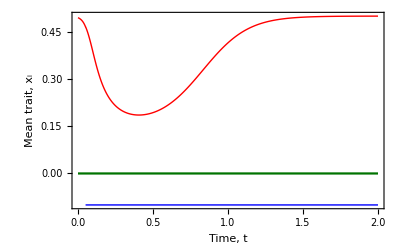

```mathematica
yMax=0.6;
x10List={};Do[x10List=Append[x10List,(x1a/.par)((N1a[t]/. sol01)[[1]])/((N1a[t]/. sol01)[[1]]+(N1A[t]/. sol01)[[1]])],{t,0,tend01,tend01/100}];
Do[x10List=Append[x10List,(x1a/.par)((N1a[t]/. sol02)[[1]])/((N1a[t]/. sol02)[[1]]+(N1A[t]/. sol02)[[1]])],{t,0,tend02,tend02/(100 tend02/tend01)}];
x20List={};Do[x20List=Append[x20List,NA],{t,0,tend01,tend01/100}];
x21List={};Do[x21List=Append[x21List,x2/.par],{t,0,tend02,tend02/(100 tend02/tend01)}];
x2List=Flatten[{x20List,x21List}];

ListPlot[
{zeroList,x10List,x2List},Joined->True,
PlotRange->{All, All},DataRange-> {0,tMax},
PlotStyle->{RGBColor[0,0.45,0],{Red,Thick},{Blue,Thick}},Frame->True,FrameLabel->{{RawBoxes[RowBox[{RowBox[{"Mean"," ","trait"}],","," ",StyleBox[SubscriptBox["x","i"],FontSlant->"Italic"]}]],None},{RawBoxes[RowBox[{"Time",","," ",StyleBox["t",FontSlant->"Italic"]}]],None}},LabelStyle->{FontFamily->"Arial",18,GrayLevel[0]}
]
```

## Simulation of the continuous-time Lotka-Volterra model (Late immigration of sp. 2)

```mathematica
par={x1a->0.5,x1A->0,x2->-0.1,xopt->0,rMax01->100,rMax02->100,betaMax->1.1};
var={N1a->N1a[t],N1A->N1A[t],N2->N2[t]};
```

```mathematica
(* population dynamics *)
f1=dN1adt/.var;
f2=dN1Adt/.var;
f3=dN2dt/.var;
```

```mathematica
tend01=0.1;tMax=2;

(* initial values *)
init={N1a[0]==0.99(rMax01 Exp[-x1a^2]/.par),N1A[0]==0.01(rMax01 Exp[-x1a^2]/.par),N2[0]==0.};
flow={N1a'[t]==f1/.par,N1A'[t]==f2/.par,N2'[t]==f3/.par};

(* simulation *)
sol01=NDSolve[Join[flow,init],{N1a,N1A,N2},{t,0,tend01}];
```

```mathematica
tend02=tMax-tend01;

(* initial values *)
init={N1a[0]==(N1a[tend01]/.sol01)[[1]],N1A[0]==(N1A[tend01]/.sol01)[[1]],N2[0]==((N1a[tend01]/.sol01)[[1]]+(N1A[tend01]/.sol01)[[1]])/9};
flow={N1a'[t]==f1/.par,N1A'[t]==f2/.par,N2'[t]==f3/.par};

(* simulation *)
sol02=NDSolve[Join[flow,init],{N1a,N1A,N2},{t,0,tend02}];
```

```mathematica
N1aList={};Do[N1aList=Append[N1aList,(N1a[t]/. sol01)[[1]]],{t,0,tend01,tend01/100}];
Do[N1aList=Append[N1aList,(N1a[t]/. sol02)[[1]]],{t,0,tend02,tend02/(100 tend02/tend01)}];
N1AList={};Do[N1AList=Append[N1AList,(N1A[t]/. sol01)[[1]]],{t,0,tend01,tend01/100}];
Do[N1AList=Append[N1AList,(N1A[t]/. sol02)[[1]]],{t,0,tend02,tend02/(100 tend02/tend01)}];
N2List={};
Do[N2List=Append[N2List,NA],{t,0,tend01,tend01/100}];
Do[N2List=Append[N2List,(N2[t]/. sol02)[[1]]],{t,0,tend02,tend02/(100 tend02/tend01)}];
zeroList={};
Do[zeroList=Append[zeroList,0],{t,100 (1+tend02/tend01) }];
```

### Population dynamics

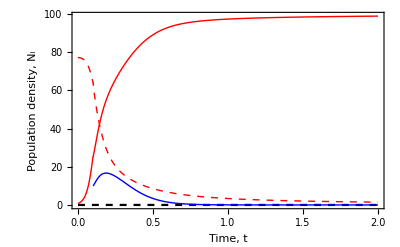

```mathematica
yMax=100;
ListPlot[
{zeroList,N1AList,N1aList,N2List},DataRange-> {0,tMax},
PlotStyle->{{Black,Dashed},{Red,Thick},{Red,Dashed,Thick},{Blue,Thick}},Joined->True,Frame->True,FrameLabel->{{RawBoxes[RowBox[{RowBox[{"Population"," ","density"}],","," ",StyleBox[SubscriptBox["N","i"],FontSlant->"Italic"]}]],None},{RawBoxes[RowBox[{"Time",","," ",StyleBox["t",FontSlant->"Italic"]}]],None}},LabelStyle->{FontFamily->"Arial",18,GrayLevel[0]}
]
```

### Mean trait dynamics

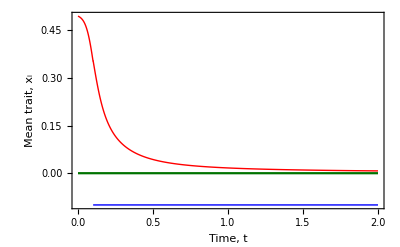

```mathematica
yMax=0.6;
x10List={};Do[x10List=Append[x10List,(x1a/.par)((N1a[t]/. sol01)[[1]])/((N1a[t]/. sol01)[[1]]+(N1A[t]/. sol01)[[1]])],{t,0,tend01,tend01/100}];
Do[x10List=Append[x10List,(x1a/.par)((N1a[t]/. sol02)[[1]])/((N1a[t]/. sol02)[[1]]+(N1A[t]/. sol02)[[1]])],{t,0,tend02,tend02/(100 tend02/tend01)}];
x20List={};Do[x20List=Append[x20List,NA],{t,0,tend01,tend01/100}];
x21List={};Do[x21List=Append[x21List,x2/.par],{t,0,tend02,tend02/(100 tend02/tend01)}];
x2List=Flatten[{x20List,x21List}];

ListPlot[
{zeroList,x10List,x2List},Joined->True,
PlotRange-> {All,All},DataRange-> {0,tMax},
PlotStyle->{RGBColor[0,0.45,0],{Red,Thick},{Blue,Thick}},Frame->True,FrameLabel->{{RawBoxes[RowBox[{RowBox[{"Mean"," ","trait"}],","," ",StyleBox[SubscriptBox["x","i"],FontSlant->"Italic"]}]],None},{RawBoxes[RowBox[{"Time",","," ",StyleBox["t",FontSlant->"Italic"]}]],None}},LabelStyle->{FontFamily->"Arial",18,GrayLevel[0]}
]
```